# 1/FPR Plots for Deepsets

```mathematica
Get["https://raw.githubusercontent.com/mark-caprio/CustomTicks/master/CustomTicks.m"]
```

```mathematica
(*Functions to compute the inverse FPRs and their respective errors*)
invertedFPR[fpr_] := 1/fpr
σinvertedFPR[fpr_, σfpr_] := σfpr/fpr^2
```

## FPRs

```mathematica
FPRs = 
<|"16bits" -> {0.2923, 0.2127, 0.1662, 0.2326, 0.1074}, 
 "15bits" -> {0.2890, 0.2150, 0.1715, 0.2323, 0.1074},
 "14bits" -> {0.2880, 0.2101, 0.1646, 0.2274, 0.1066},
 "13bits" -> {0.2888, 0.2116, 0.1656, 0.2291, 0.1071},
 "12bits" -> {0.2909, 0.2129, 0.1704, 0.2310, 0.1069},
 "11bits" -> {0.2880, 0.2123, 0.1668, 0.2283, 0.1067},
 "10bits" -> {0.2920, 0.2135, 0.1696, 0.2312, 0.1078},
 "9bits" -> {0.2871, 0.2103, 0.1650, 0.2361, 0.1056},
 "8bits" -> {0.2907, 0.2128, 0.1696, 0.2311, 0.1060},
 "7bits" -> {0.2919, 0.2124, 0.1715, 0.2307, 0.1071},
 "6bits" -> {0.2910, 0.2127, 0.1738, 0.2270, 0.1071},
 "5bits" -> {0.3002, 0.2166, 0.1795, 0.2373, 0.1092},
 "4bits" -> {0.3061, 0.2241, 0.1984, 0.2529, 0.1139},
 "3bits" -> {0.3355, 0.2406, 0.2722, 0.2877, 0.1250},
 "2bits" -> {0.5111, 0.3030, 0.3871, 0.4321, 0.1968}
|>;
σFPRs = 
<|"16bits" -> {0.0021, 0.0024, 0.0032, 0.0051, 0.0013}, 
 "15bits" -> {0.0014, 0.0071, 0.0081, 0.0052, 0.0014},
 "14bits" -> {0.0038, 0.0018, 0.0030, 0.0030, 0.0004},
 "13bits" -> {0.0022, 0.0019, 0.0031, 0.0041, 0.0014},
 "12bits" -> {0.0031, 0.0017, 0.0039, 0.0045, 0.0016},
 "11bits" -> {0.0021, 0.0011, 0.0058, 0.0048, 0.0010},
 "10bits" -> {0.0013, 0.0012, 0.0032, 0.0027, 0.0007},
 "9bits" -> {0.0033, 0.0026, 0.0022, 0.0040, 0.0022},
 "8bits" -> {0.0021, 0.0010, 0.0059, 0.0026, 0.0005},
 "7bits" -> {0.0040, 0.0034, 0.0063, 0.0055, 0.0016},
 "6bits" -> {0.0017, 0.0024, 0.0064, 0.0045, 0.0016},
 "5bits" -> {0.0102, 0.0039, 0.0036, 0.0113, 0.0034},
 "4bits" -> {0.0043, 0.0064, 0.0089, 0.0090, 0.0028},
 "3bits" -> {0.0160, 0.0071, 0.0690, 0.0153, 0.0048},
 "2bits" -> {0.0819, 0.0076, 0.0529, 0.0800, 0.0225}
|>;
```

```mathematica
invertedFPRs = invertedFPR /@ FPRs;
σinvertedFPRs = MapThread[σinvertedFPR[#1, #2]&,{FPRs,σFPRs}];
```

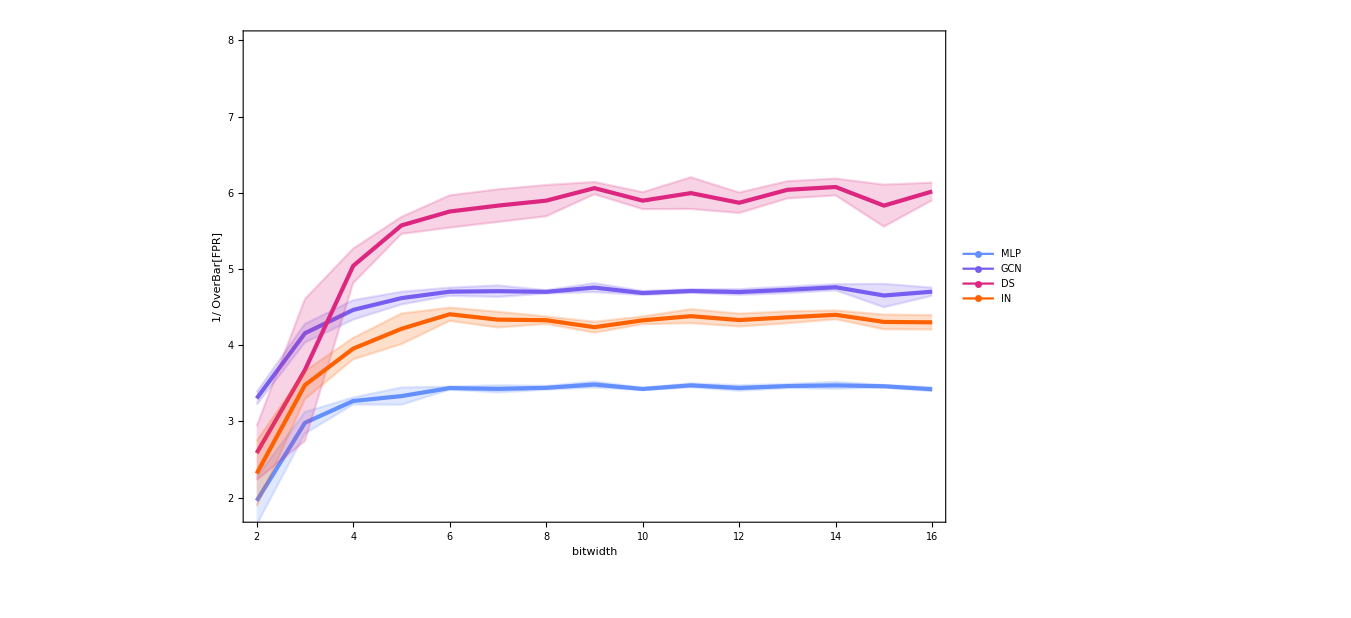

```mathematica
gluonFPRs = Sort@Table[{Length@invertedFPRs[[All, 1]]+2 - i,invertedFPRs[[i, 1]]},{i, 1, Length@invertedFPRs[[All, 1]]}];
gluonFPRsBot = Sort@Table[{Length@invertedFPRs[[All, 1]]+2 - i,invertedFPRs[[i, 1]] - σinvertedFPRs[[i, 1]]},{i, 1, Length@invertedFPRs[[All, 1]]}];
gluonFPRsTop = Sort@Table[{Length@invertedFPRs[[All, 1]]+2 - i,invertedFPRs[[i, 1]] + σinvertedFPRs[[i, 1]]},{i, 1, Length@invertedFPRs[[All, 1]]}];

quarkFPRs = Sort@Table[{Length@invertedFPRs[[All, 2]]+2 - i,invertedFPRs[[i, 2]]},{i, 1, Length@invertedFPRs[[All, 2]]}];
quarkFPRsBot = Sort@Table[{Length@invertedFPRs[[All, 2]]+2 - i,invertedFPRs[[i, 2]] - σinvertedFPRs[[i, 2]]},{i, 1, Length@invertedFPRs[[All, 1]]}];
quarkFPRsTop = Sort@Table[{Length@invertedFPRs[[All, 2]]+2 - i,invertedFPRs[[i, 2]] + σinvertedFPRs[[i, 2]]},{i, 1, Length@invertedFPRs[[All, 1]]}];

wFPRs = Sort@Table[{Length@invertedFPRs[[All, 3]]+2 - i,invertedFPRs[[i, 3]]},{i, 1, Length@invertedFPRs[[All, 1]]}];
wFPRsBot = Sort@Table[{Length@invertedFPRs[[All, 3]]+2 - i,invertedFPRs[[i, 3]] - σinvertedFPRs[[i, 3]]},{i, 1, Length@invertedFPRs[[All, 1]]}];
wFPRsTop = Sort@Table[{Length@invertedFPRs[[All, 3]]+2 - i,invertedFPRs[[i, 3]] + σinvertedFPRs[[i, 3]]},{i, 1, Length@invertedFPRs[[All, 1]]}];

zFPRs = Sort@Table[{Length@invertedFPRs[[All, 4]]+2 - i,invertedFPRs[[i, 4]]},{i, 1, Length@invertedFPRs[[All, 1]]}];
zFPRsBot = Sort@Table[{Length@invertedFPRs[[All, 4]]+2 - i,invertedFPRs[[i, 4]] - σinvertedFPRs[[i, 4]]},{i, 1, Length@invertedFPRs[[All, 1]]}];
zFPRsTop = Sort@Table[{Length@invertedFPRs[[All, 4]]+2 - i,invertedFPRs[[i, 4]] + σinvertedFPRs[[i, 4]]},{i, 1, Length@invertedFPRs[[All, 1]]}];

topFPRs = Sort@Table[{Length@invertedFPRs[[All, 5]]+2 - i,invertedFPRs[[i, 5]]},{i, 1, Length@invertedFPRs[[All, 1]]}];
topFPRsBot = Sort@Table[{Length@invertedFPRs[[All, 5]]+2 - i,invertedFPRs[[i, 5]] - σinvertedFPRs[[i, 5]]},{i, 1, Length@invertedFPRs[[All, 1]]}];
topFPRsTop = Sort@Table[{Length@invertedFPRs[[All, 5]]+2 - i,invertedFPRs[[i, 5]] + σinvertedFPRs[[i, 5]]},{i, 1, Length@invertedFPRs[[All, 1]]}];

hexColors = {"#648FFF","#785EF0","#DC267F","#FE6100","#FFB000", "#B2A080"};
hexColors = Map[RGBColor, hexColors];
lighterHexColors = {#, Opacity[0.2]}&/@hexColors;
darkerHexColors = {Darker[#,0.2]}&/@hexColors;

padding = {{90, 90},{90, 90}};

Needs["CustomTicks`"]
SetOptions[LinTicks,TickLengthScale->1.5];
bitPlot =Show[
ListLinePlot[gluonFPRs,PlotStyle->{hexColors[[1]], Thickness[0.003]}, PlotRange->All],
ListPlot[{gluonFPRsTop,gluonFPRsBot},
PlotStyle->{lighterHexColors[[1]], lighterHexColors[[1]]},Joined->True, Filling->{1->{2}}, FillingStyle->lighterHexColors[[1]],PlotRange->All],
ListLinePlot[quarkFPRs,PlotStyle->{hexColors[[2]], Thickness[0.003]}, PlotRange->All],
ListPlot[{quarkFPRsTop,quarkFPRsBot},
PlotStyle->{lighterHexColors[[2]], lighterHexColors[[2]]},Joined->True, Filling->{1->{2}}, FillingStyle->lighterHexColors[[1]],PlotRange->All],
ListLinePlot[wFPRs,PlotStyle->{hexColors[[3]], Thickness[0.003]}, PlotRange->All],
ListPlot[{wFPRsTop,wFPRsBot},
PlotStyle->{lighterHexColors[[3]], lighterHexColors[[3]]},Joined->True, Filling->{1->{2}}, FillingStyle->lighterHexColors[[1]],PlotRange->All],
ListLinePlot[zFPRs,PlotStyle->{hexColors[[4]], Thickness[0.003]}, PlotRange->All],
ListPlot[{zFPRsTop,zFPRsBot},
PlotStyle->{lighterHexColors[[4]], lighterHexColors[[4]]},Joined->True, Filling->{1->{2}}, FillingStyle->lighterHexColors[[1]],PlotRange->All],
ImageSize->1000, ImageResolution->300,ImagePadding->padding,
Frame->True, FrameStyle->Directive[20, Black], FrameLabel->{Row[{Spacer@750, "bitwidth"}],Row[{Spacer@450, "1/"OverBar["FPR"]}]}, FrameTicksStyle->Directive[Black, AbsoluteThickness[1.5], FontSize->20],FrameTicks->{{LinTicks,StripTickLabels[LinTicks]},{LinTicks,StripTickLabels[LinTicks]}},
PlotRange->{{2,16},{1.8, 8}}, PlotRangePadding->{.3, 0.4} ];
legendBitPlot = Legended[bitPlot,Placed[LineLegend[{hexColors[[1]], hexColors[[2]], hexColors[[3]], hexColors[[4]]}, {"MLP", "GCN",  "DS", "IN"}, LegendMarkers->Graphics[{Thickness[.3], Line[{{0,0},{10,0}}]}],LabelStyle->{20, Bold}, LegendFunction->(Panel[#,Background->White] &)],{0.1,0.8}]]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["deepsets_bit_plot.pdf",legendBitPlot]
```

/Users/neutron/olgpu/ki/bin/trained_deepsets/bitsweep

deepsets_bit_plot.pdf